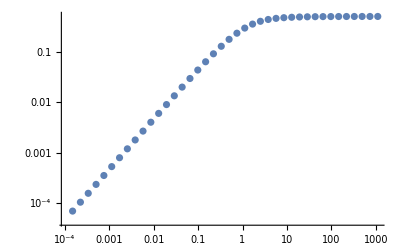

```mathematica
SetDirectory[NotebookDirectory[]];
ListLogLogPlot[Import["Earth-Geo/I-year-Borexino.m"]]
```

## Setup

```mathematica
fluxHNLall=Import["N-Specs/fluxHNL-all.m"];
fluxHNLe=Import["N-Specs/fluxHNL-e.m"];
fluxHNLμ=Import["N-Specs/fluxHNL-mu.m"];
fluxHNLτ=Import["N-Specs/fluxHNL-tau.m"];
sawTooth=2(EγMax-Eγ)/(EγMax-EγMin)^2 UnitStep[EγMax-Eγ,Eγ-EγMin];
ℐinterpBXNO=Interpolation[Import["Earth-Geo/I-year-Borexino.m"]];
ℐinterpSK=Interpolation[Import["Earth-Geo/I-year-SK.m"]];
ℐBXNO[x_]:= (ℐinterpBXNO[0.0001]/0.0001 )x   + UnitStep[x-0.001](ℐinterpBXNO[x] -(ℐinterpBXNO[0.0001]/0.0001 )x) + UnitStep[x-1000](ℐinterpBXNO[1000] -ℐinterpBXNO[x] ) ;
ℐSK[x_]:= (ℐinterpSK[0.0001]/0.0001 )x   + UnitStep[x-0.001](ℐinterpSK[x] -(ℐinterpSK[0.0001]/0.0001 )x) + UnitStep[x-1000](ℐinterpSK[1000] -ℐinterpSK[x] ) ;
ΦνSolar= 6.538802954197485*10^10;
dRef=1.97 10^-9(* MeV^-1 *) 197 (* MeV fm *) 10^-13(* fm per cm  *);
Zref=12;
overallNormalization= α ΦνSolar dRef^2 10^30/.α-> 1/137;
VnARef=10^30;
overallNormalization
```

0.718857

```mathematica
evalIntegral[EEγ_,mNN_,dd_, SawOrBox_,flav_,expt_]:=Block[{mN,Eν,Eγ,EγMax,EγMin,tri,λ,box,dist,fluxHNL,ℐ},
If[flav=="all",fluxHNL=fluxHNLall];
If[flav=="e",fluxHNL=fluxHNLe];
If[flav=="μ",fluxHNL=fluxHNLμ];
If[flav=="τ",fluxHNL=fluxHNLτ];
tri=sawTooth/. {EγMin->Eν/2(1-√(1-mN^2/Eν^2)),EγMax->Eν/2(1+√(1-mN^2/Eν^2)) }; 
box=1/(EγMax-EγMin)UnitStep[EγMax-Eγ,Eγ-EγMin]/. {EγMin->Eν/2(1-√(1-mN^2/Eν^2)),EγMax->Eν/2(1+√(1-mN^2/Eν^2)) }; 
If[SawOrBox=="Saw",dist=tri,dist=box];
λ=1/dd^2 Eν/10(1/mN)^4 √(0.99/(1-mN^2/Eν^2));
If[expt=="SK",ℐ=ℐSK];
If[expt=="BXNO",ℐ=ℐBXNO];
NIntegrate[Evaluate[ℐ[1/λ] fluxHNL dist/.{mN-> mNN,Eγ-> EEγ}],{Eν,mNN,18.8},Method->{Automatic,"SymbolicProcessing"-> 0},PrecisionGoal->6]     ];
```

```mathematica
getRate[mNN_,dd_,EγMin_,EγMax_,bins_,SawOrBox_,flav_,expt_]:= Block[{Eν,mN,sawIntegrand,binWidth},binWidth=(EγMax -EγMin)/bins;
dd^2 overallNormalization

    (binWidth Sum[evalIntegral[Eγ,mNN,dd,SawOrBox,flav,expt],{Eγ,EγMin+binWidth, EγMax-binWidth,binWidth}]+ 1/2 binWidth(evalIntegral[EγMin,mNN,dd,SawOrBox,flav,expt]+evalIntegral[EγMax,mNN,dd,SawOrBox,flav,expt]))
]
```

```mathematica
findSolLERI[mNN_,dGuess_,SawOrBox_,flav_]:=Block[{ratePer100Tonne,numSecInDay,densityLiqSint,fidVol,nA,Zeff,res,d0,dd,prediction},
ratePer100Tonne=60; (* 0.1 events/100 t/day / keV * (800 keV- 200 keV) = 600 keV * 0.1 events/100 t/day/ keV  *)
numSecInDay=60 60 24;
densityLiqSint=876 (* kg/m3*)*  0.001 (* tonne/kg*) /10^6 (* cm^3/m^3*)//N ;(* from http://borex.lngs.infn.it/Thesis/M.Leung_PhD_Thesis.pdf*) 
fidVol=100 (*tonne*) / densityLiqSint;
nA=1.01 10^23(* cm^-3 *);
Zeff=11.8;
res=1;
d0=dGuess/.mN-> mNN;
dd=d0;
prediction=2;
While[Abs[prediction-1]>10^-3,prediction=(104 (*Hz*) numSecInDay (* s in day*) )/ratePer100Tonne((fidVol nA)/10^30)(Zeff/12)^2 getRate[mNN,dd,0.2,0.8,15,SawOrBox,flav,"BXNO"] //Quiet;
If[prediction==0,prediction=1];
dd=If[mNN^3 dd^2>1, (1/prediction)^(1/2)dd , (1/prediction)^(1/4)dd];
];
dd
]

findSolLERII[mNN_,dGuess_,SawOrBox_,flav_]:=Block[{ratePer100Tonne,numSecInDay,densityLiqSint,fidVol,nA,Zeff,res,d0,dd,prediction},
ratePer100Tonne=17; (* 0.01 events/day/100 t/ keV * (2500 keV-800 keV) *)
numSecInDay=60 60 24;
densityLiqSint=876 (* kg/m3*)*  0.001 (* tonne/kg*) /10^6 (* cm^3/m^3*)//N ;(* from http://borex.lngs.infn.it/Thesis/M.Leung_PhD_Thesis.pdf*) 
fidVol=100 (*tonne*) / densityLiqSint;
nA=1.01 10^23(* cm^-3 *);
Zeff=11.8;
res=1;
d0=dGuess/.mN-> mNN;
dd=d0;
prediction=2;
While[Abs[prediction-1]>10^-3,
prediction=(104 (*Hz*) numSecInDay (* s in day*) )/ratePer100Tonne((fidVol nA)/10^30)(Zeff/12)^2
getRate[mNN,dd,0.8,2.5,15,SawOrBox,flav,"BXNO"] //Quiet;
If[prediction==0,predd=1];
dd=If[mNN^3 dd^2>1, (1/prediction)^(1/2)dd , (1/prediction)^(1/4)dd]
];
dd
]

findSolSK[mNN_,dGuess_,SawOrBox_,flav_]:=Block[{numSecInDay,densityH20,fidVolSK,nA,Zeff,res,d0,dd,prediction,rateBoundSK},
numSecInDay=60 60 24;
densityH20=1 (* g/cm3*)*  0.001 (* tonne/kg*) 0.001 (* kg/g*)//N ;(* from http://borex.lngs.infn.it/Thesis/M.Leung_PhD_Thesis.pdf*) 
fidVolSK=22.5 10^3 (*tonne*) / densityH20;
nA=1.01 10^23(* cm^-3 *);
Zeff=11.8;
rateBoundSK=4.62 22.5; (* 4.62 events/kton/day * 22.5 kton * 1 day*)
res=1;
d0=dGuess/.mN-> mNN;
dd=d0;
prediction=2;
While[Abs[prediction-1]>10^-3,prediction=(104 (*Hz*) numSecInDay (* s in day*) )/rateBoundSK((fidVolSK nA)/10^30)(Zeff/12)^2 getRate[mNN,dd,4.49, 15.5,15,SawOrBox,flav,"SK"] //Quiet;
If[prediction==0,prediction=1];
dd=If[mNN^3 dd^2>1, (1/prediction)^(1/2)dd , (1/prediction)^(1/4)dd]
];
dd
]
```

## Constraint Curves

```mathematica
mNTabLERI=Join[Table[0.05 1.5^n,{n,0,7}],Table[n,{n,0.6,2,0.05}],Table[n,{n,2.5,7.5,0.5}]];
mNTabLERII=Join[Table[0.05 1.5^n,{n,0,7}],Table[n,{n,0.6,2,0.05}],Table[n,{n,2.5,12,0.5}]];
mNTabSK=Join[Table[0.05 1.5^n,{n,0,7}],Table[n,{n,0.9,2,0.05}],Table[n,{n,2.5,18.8,0.5}]];
```

### Saw

```mathematica
ddGuessLERIsaw=Import["Guess-Curves/BRXNO-LERI-Saw.m"];
ddGuessLERIIsaw=Import["Guess-Curves/BRXNO-LERII-Saw.m"];
ddGuessSKsaw=Import["Guess-Curves/BRXNO-SK-Saw.m"];
```

```mathematica
solTabLERIsawAll=SortBy[First]@Table[{mN,findSolLERI[mN,ddGuessLERIsaw,"Saw","all"]},{mN,mNTabLERI}];
solTabLERIIsawAll=SortBy[First]@Table[{mN,findSolLERII[mN,ddGuessLERIIsaw,"Saw","all"]},{mN,mNTabLERII}];
solTabSKsawAll=SortBy[First]@Table[{mN,findSolSK[mN,ddGuessSKsaw,"Saw","all"]},{mN,mNTabSK}];
```

```mathematica
solTabLERIsawe=SortBy[First]@Table[{mN,findSolLERI[mN,ddGuessLERIsaw,"Saw","e"]},{mN,mNTabLERI}];
solTabLERIIsawe=SortBy[First]@Table[{mN,findSolLERII[mN,ddGuessLERIIsaw,"Saw","e"]},{mN,mNTabLERII}];
solTabSKsawe=SortBy[First]@Table[{mN,findSolSK[mN,ddGuessSKsaw,"Saw","e"]},{mN,mNTabSK}];
```

```mathematica
solTabLERIsawμ=SortBy[First]@Table[{mN,findSolLERI[mN,ddGuessLERIsaw,"Saw","μ"]},{mN,mNTabLERI}];
solTabLERIIsawμ=SortBy[First]@Table[{mN,findSolLERII[mN,ddGuessLERIIsaw,"Saw","μ"]},{mN,mNTabLERII}];
solTabSKsawμ=SortBy[First]@Table[{mN,findSolSK[mN,ddGuessSKsaw,"Saw","μ"]},{mN,mNTabSK}];
```

```mathematica
solTabLERIsawτ=SortBy[First]@Table[{mN,findSolLERI[mN,ddGuessLERIsaw,"Saw","τ"]},{mN,mNTabLERI}];
solTabLERIIsawτ=SortBy[First]@Table[{mN,findSolLERII[mN,ddGuessLERIIsaw,"Saw","τ"]},{mN,mNTabLERII}];
solTabSKsawτ=SortBy[First]@Table[{mN,findSolSK[mN,ddGuessSKsaw,"Saw","τ"]},{mN,mNTabSK}];
```

### Box

```mathematica
ddGuessLERIBox=Import["Guess-Curves/BRXNO-LERI-Box.m"];
ddGuessLERIIBox=Import["Guess-Curves/BRXNO-LERII-Box.m"];
ddGuessSKBox=Import["Guess-Curves/BRXNO-SK-Box.m"];
```

```mathematica
solTabLERIBoxAll=SortBy[First]@Table[{mN,findSolLERI[mN,ddGuessLERIBox,"Box","all"]},{mN,mNTabLERI}];
solTabLERIIBoxAll=SortBy[First]@Table[{mN,findSolLERII[mN,ddGuessLERIIBox,"Box","all"]},{mN,mNTabLERII}];
solTabSKBoxAll=SortBy[First]@Table[{mN,findSolSK[mN,ddGuessSKBox,"Box","all"]},{mN,mNTabSK}];
```

```mathematica
solTabLERIBoxe=SortBy[First]@Table[{mN,findSolLERI[mN,ddGuessLERIBox,"Box","e"]},{mN,mNTabLERI}];
```

```mathematica
solTabLERIBoxμ=SortBy[First]@Table[{mN,findSolLERI[mN,ddGuessLERIBox,"Box","μ"]},{mN,mNTabLERI}];
```

```mathematica
solTabLERIBoxτ=SortBy[First]@Table[{mN,findSolLERI[mN,ddGuessLERIBox,"Box","τ"]},{mN,mNTabLERI}];
```

```mathematica
solTabLERIBoxe=SortBy[First]@Table[{mN,findSolLERI[mN,ddGuessLERIBox,"Box","e"]},{mN,mNTabLERI}];
solTabLERIIBoxe=SortBy[First]@Table[{mN,findSolLERII[mN,ddGuessLERIIBox,"Box","e"]},{mN,mNTabLERII}];
solTabSKBoxe=SortBy[First]@Table[{mN,findSolSK[mN,ddGuessSKBox,"Box","e"]},{mN,mNTabSK}];
```

```mathematica
solTabLERIBoxμ=SortBy[First]@Table[{mN,findSolLERI[mN,ddGuessLERIBox,"Box","μ"]},{mN,mNTabLERI}];
solTabLERIIBoxμ=SortBy[First]@Table[{mN,findSolLERII[mN,ddGuessLERIIBox,"Box","μ"]},{mN,mNTabLERII}];
solTabSKBoxμ=SortBy[First]@Table[{mN,findSolSK[mN,ddGuessSKBox,"Box","μ"]},{mN,mNTabSK}];
```

```mathematica
solTabLERIBoxτ=SortBy[First]@Table[{mN,findSolLERI[mN,ddGuessLERIBox,"Box","τ"]},{mN,mNTabLERI}];
solTabLERIIBoxτ=SortBy[First]@Table[{mN,findSolLERII[mN,ddGuessLERIIBox,"Box","τ"]},{mN,mNTabLERII}];
solTabSKBoxτ=SortBy[First]@Table[{mN,findSolSK[mN,ddGuessSKBox,"Box","τ"]},{mN,mNTabSK}];
```

### Excl curves dictionary

```mathematica
SKdict=<|
"Saw"-> <|"all"-> solTabSKsawAll, "e"-> solTabSKsawe,  "μ"->solTabSKsawμ, "τ"->solTabSKsawτ|>, "Box"-> <|"all"-> solTabSKBoxAll, "e"-> solTabSKBoxe,  "μ"->solTabSKBoxμ, "τ"->solTabSKBoxτ|> |>;
LERIdict=<|
"Saw"-> <|"all"-> solTabLERIsawAll, "e"-> solTabLERIsawe,  "μ"->solTabLERIsawμ, "τ"->solTabLERIsawτ|>, "Box"-> <|"all"-> solTabLERIBoxAll, "e"-> solTabLERIBoxe,  "μ"->solTabLERIBoxμ, "τ"->solTabLERIBoxτ|> |>;
LERIIdict=<|
"Saw"-> <|"all"-> solTabLERIIsawAll, "e"-> solTabLERIIsawe,  "μ"->solTabLERIIsawμ, "τ"->solTabLERIIsawτ|>, "Box"-> <|"all"-> solTabLERIIBoxAll, "e"-> solTabLERIIBoxe,  "μ"->solTabLERIIBoxμ, "τ"->solTabLERIIBoxτ|> |>;

exclCurves=<| "LERI"-> LERIdict, "LERII"-> LERIIdict,"SK"-> SKdict|>;
Export["Exclusion-Curves/exclCurves.m",exclCurves];
```

```mathematica
Export["Exclusion-Curves/left-point-plot.m",{0.01,findSolLERI[0.01,(ddGuessLERIBox/.mN-> 0.01),"Box","all"]}];
```

```mathematica
LogLogPlot[{Max[dLLExclLSK,dGGExclSK],Max[dLLExclLERI,dGGExclLERI],Max[dLLExclLERII,dGGExclLERII],decEqRadEarth},{mN,0.05,25},PlotRange->{10^-13,10^-7},Frame-> True,FrameStyle->Black,PlotStyle->{Automatic,Dashed,DotDashed,{Dotted,Thick,Black}},
Epilog->{Inset[Rotate[Style["c τ = R_⊕",13],-0.4],{-0.25,-20.0}]},PlotLegends->Placed[{"SK-IV","Borexino LER-I","Borexino LER-II"},{0.3,0.175}],FrameLabel->(Style[#,14]&)/@{"m_N   [MeV]","d_eff    [MeV^-1]"},PlotRangePadding->0]//Quiet
```